## Definitions:

```mathematica
(*Parallel Energy*)
Ekp[M_,z_]:=Sqrt[M^2+z^2];

(*Total Energy*)
Ekr[x_,y_,z_,q_,M_,r_]:=Sqrt[x^2+y^2+z^2+q^2/4+M^2+(-1)^(r-1)*q*Ekp[M,z]];
(*p=0 Case*)
Ekp0byM[Q_,r_]:=Sqrt[Q^2/4+1+(-1)^(r-1)*Q];
(*p^(1,2)=0 & p^3=M Case*)
Ekp3byM[Q_,r_]:=Sqrt[2+Q^2/4+(-1)^(r-1)*Q*Sqrt[2]];
(*Subscript[p, T]=M & p^3=M Case*)
EkpbyM[Q_,r_]:=Sqrt[3+Q^2/4+(-1)^(r-1)*Q*Sqrt[2]];
DEkr[x_,y_,z_,Q_,zt_,r_]:=Sqrt[x^2+y^2+z^2+Q^2/4+zt^2+(-1)^(r-1)*Q*Ekp[zt,z]];(*As compared to the previous case, here (x,y,z) are dimensionless quantities: (p^1/T,p^2/T,p^3/T)*)
```

## Functions:

```mathematica
energy=ParallelTable[{i,1.Ekp0byM[i,1],1. Ekp3byM[i,1],1. EkpbyM[i,1],1.Ekp0byM[i,2],1. Ekp3byM[i,2],1. EkpbyM[i,2]},{i,0,10,0.001}]//Quiet;
```

## Plots:

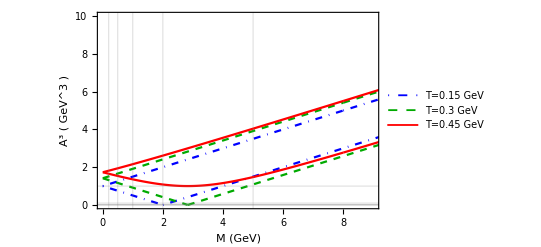
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListPlot[{energy[[All,{1,2}]],energy[[All,{1,3}]],energy[[All,{1,4}]],energy[[All,{1,5}]],energy[[All,{1,6}]],energy[[All,{1,7}]]},
GridLines->{{0.2,0.5,1,2,5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0,9},{0.0003,10}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["M   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*T=0.15 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*T=0.3 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*T=0.45 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

## Export:

```mathematica
Export["C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/energy.csv",energy,"CSV"]
```

C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/energy.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/energy.csv"]]]
```